```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Critical-region/critical_region/LPAp/UV500/nu/NLOdata

# T_scaling

## data

```mathematica
fpi=Flatten[Import["../LPAp_mub0/buffer/mSigma.dat"]];
Zphi=Flatten[Import["../LPAp_mub0/buffer/Zphi.dat"]];
fpi=fpi*√Zphi;
T0=Flatten[Import["../LPAp_mub0/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["../LPAp_mub500/buffer/mSigma.dat"]];
Zphi=Flatten[Import["../LPAp_mub500/buffer/Zphi.dat"]];
fpi=fpi*√Zphi;
T0=Flatten[Import["../LPAp_mub500/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub500=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1mub500=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub500linear=Transpose[{T0[[2;;Length[t]-2]],-Flatten[Table[FindFit[datamub500[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
```

## Fit

```mathematica
(*A=Exp[1.532];*)
δ=4.79;
delta=4.79;
beta=0.397;
nu=0.759;
omega=0.6745;
θt=nu*omega;
fitfun=A x^β(1+cm x^θt1);
fitfun2=A+ν x+Log[(1+cm Exp[x]^θt)];
```

```mathematica
fitnu=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[-NonlinearModelFit[datamub0[[i-1;;i+1]],fitfun2,{A,ν,cm},x][[1]][[2]][[2]][[2]],{i,2,Length[t]-2}]]}];
```

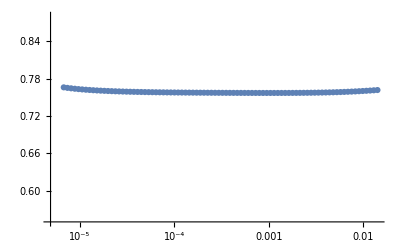

```mathematica
Show[ListPlot[fitnu,ScalingFunctions->{"Log"},PlotRange->{All,{0.55,0.88}}]]
```

```mathematica
Export["./NLOnu.dat",fitnu]
```

./NLOnu.dat

```mathematica
fittheta=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[NonlinearModelFit[datamub0[[i-1;;i+1]],fitfun2,{A,ν,cm},x][[1]][[2]][[3]][[2]],{i,2,Length[t]-2}]]}];
```

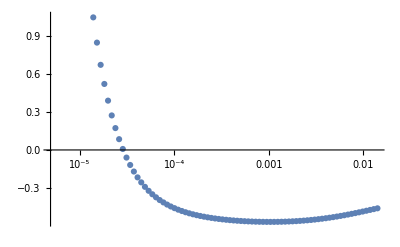

```mathematica
ListPlot[fittheta,ScalingFunctions->{"Log"}]
```

## Fit mub

```mathematica
(*A=Exp[1.532];*)
δ=4.79;
delta=4.79;
beta=0.397;
nu=0.759;
omega=0.6745;
θt=nu*omega;
fitfun=A x^β(1+cm x^θt1);
fitfun2=A+ν x+Log[(1+cm Exp[x]^θt)];
```

```mathematica
fitnumub500=Transpose[{-t[[2;;Length[t]-2]],Flatten[Table[-NonlinearModelFit[datamub500[[i-1;;i+1]],fitfun2,{A,ν,cm},x][[1]][[2]][[2]][[2]],{i,2,Length[t]-2}]]}];
```

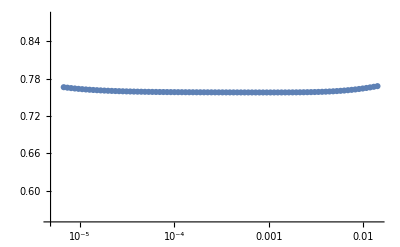

```mathematica
Show[ListPlot[fitnumub500,ScalingFunctions->{"Log"},PlotRange->{All,{0.55,0.88}}]]
```

```mathematica
Export["./NLOnumub500.dat",fitnumub500]
```

./NLOnumub500.dat